```mathematica
thz2waavenum
```

33.3564

```mathematica
33*thz2waavenum
30*thz2waavenum
```

1100.76

1000.69

```mathematica
thz2waavenum=1/0.0299792458;SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
phDOSfiles={"1.total_dos.dat","2.total_dos.dat","3.total_dos.dat","4.total_dos.dat","5.total_dos.dat","6.total_dos.dat","7.total_dos.dat","8.total_dos.dat","9.total_dos.dat","10.total_dos.dat","11.total_dos.dat"};
fren70dos=Table[ReadList[phDOSfiles[[i]],{Number,Number}],{i,1,Length@phDOSfiles}];
```

```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/cvac_phon_dos"];
cvac=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/perf_phon_dos"];
perf=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,9}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-1126_phon_dos"];
fren1126=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-129_phon_dos"];
fren129=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-142_phon_dos"];
fren142=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-174_phon_dos"];
fren174=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/RESULTS_tom_22Aug17/phonon_dos/fren-70_phon_dos"];
fren70=Table[Partition[Flatten@Join[{ReadList[phDOSfiles[[i]],{Number,Number}],{{40,0.0},{42,0.0}}}],2],{i,1,Length@phDOSfiles}];
```

```mathematica
alatts[[6]]
```

4.73

```mathematica
names2={"Perfet Zr32C32","Frenkel Zr32C32 -- Bound Dimer","Frenkel Zr32C32 -- Bound Trimer","Frenkel Zr32C32 -- Unbound Dimer","Frenkel Zr32C32 -- Unbound Trimer","Frenkel Zr32C32 -- Unbound Tetramer","CVAC Zr32C31 - 3 C at. %"};
names={"perf","fren129","fren142","fren70","fren174","fren1126","cvac"};
objects={perf,fren129,fren142,fren70,fren174,fren1126,cvac};
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850,4.875,4.900};
vols=(alatts*2)^3/64;
fren1126Data=Table[Table[Flatten[{(fren1126[[j]][[i]][[1]]*thz2waavenum),vols[[j]],fren1126[[j]][[i]][[2]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
```

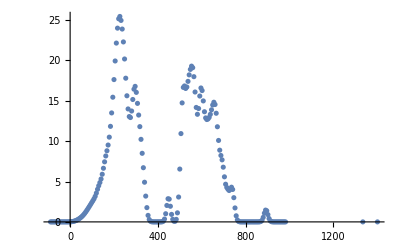

```mathematica
ListPlot@Transpose[{Transpose[fren1126Data[[1]]][[1]],Transpose[fren1126Data[[1]]][[3]]}]
```

```mathematica
fren1126Data2D=Table[Table[Flatten[{fren1126[[j]][[i]][[1]]*thz2waavenum,fren1126[[j]][[i]][[2]]+10*vols[[j]]}],{i,1,Length@fren1126[[j]]}],{j,1,Length@vols}];
data=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,vols[[j]],objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
data2D=Table[Table[Table[Flatten[{objects[[k]][[j]][[i]][[1]]*thz2waavenum,objects[[k]][[j]][[i]][[2]]}],{i,1,Length@objects[[k]][[j]]}],{j,1,Length@objects[[k]]}],{k,1,Length@objects}];
```

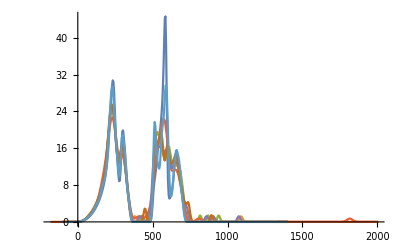

```mathematica
ListLinePlot@Table[data2D[[i]][[1]],{i,1,Length@data2D}]
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/Raman/RESULTS_Raman/"];
expRaman=ReadList[{"DCmelt011.normalised"}[[1]],{Number,Number,Number}];
```

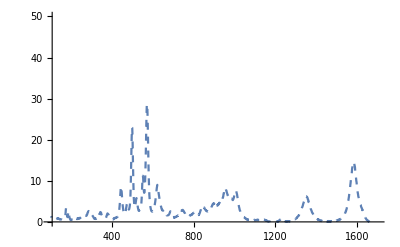

```mathematica
Show[{ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1700},{0,50}},PlotStyle->Dashed]}]
```

```mathematica
(*Raman G line at q=0 1582. *)
```

```mathematica
graphiteInt[1480]
```

0.047631

InterpolatingFunction[{{865.947, 1784.58}}, <>]

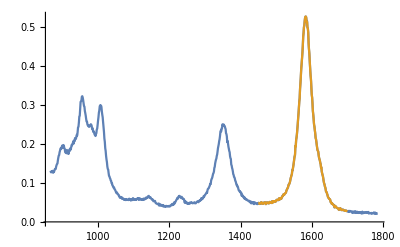

```mathematica
graphite=Transpose[{Transpose[expRaman][[1]],Transpose[expRaman][[3]]}][[210;;1020]];
graphiteInt=Interpolation[graphite]
graphiteTab=Table[{x,graphiteInt[x]},{x,1450,1700}];
graphiteP=ListLinePlot[{graphite,graphiteTab},PlotRange->All]
```

0.075007-0.0000328391 x

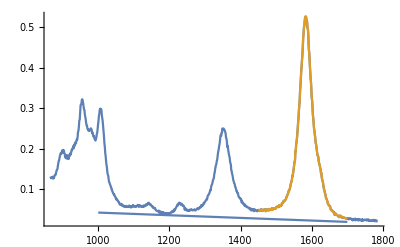

```mathematica
correction=(graphiteInt[1780]-graphiteInt[1200])/(1780-1200)*x-((graphiteInt[1780]-graphiteInt[1200])/(1780-1260)*x/.x->1200)+graphiteInt[1200]-0.01
Show[{graphiteP,Plot[correction,{x,1000,1700}]},PlotRange->All]
```

```mathematica
model[x_]:=c*PDF[CauchyDistribution[a,b],x]+g*PDF[CauchyDistribution[d,e],x]+correction
model[x]

nonlinFit=NonlinearModelFit[graphiteTab,model[x],{a,b,c,d,e,g},x,MaxIterations->10000]
nonlinFit[[1]][[2]]
```

0.075007-0.0000328391 x+c/(b π (1+(-a+x)^2/b^2))+g/(e π (1+(-d+x)^2/e^2))

FittedModel[0.075007+0.036909/(1+0.00998557 (-1619.34+x)^2)+0.50478/(1+0.00253056 (-«19»+x)^2)-0.0000328391 x]

{a→1583.08,b→19.8789,c→31.5242,d→1619.34,e→10.0072,g→1.16037}

```mathematica
nonlinFit[[1]][[2]][[1;;3]]
nonlinFit[[1]][[2]][[4;;6]]
nonlinFit[[1]][[-1]][[2]][[1]]
nonlinFit[[1]][[-1]][[2]][[2]]
```

{a→1583.08,b→19.8789,c→31.5242}

{d→1619.34,e→10.0072,g→1.16037}

0.075007

-0.0000328391 x

```mathematica
fit1=nonlinFit[[1]][[-1]][[2]][[3]]/.nonlinFit[[1]][[2]][[1;;3]]
halfmax1=(fit1/.x->a/.nonlinFit[[1]][[2]][[1]])/2
fit2=nonlinFit[[1]][[-1]][[2]][[4]]/.nonlinFit[[1]][[2]][[4;;6]]
halfmax2=(fit2/.x->d/.nonlinFit[[1]][[2]][[4]])/2
```

0.50478/(1+0.00253056 (-1583.08+x)^2)

0.25239

0.036909/(1+0.00998557 (-1619.34+x)^2)

0.0184545

{{x→1563.2},{x→1602.95}}

39.7577

1583.08

{{x→1609.34},{x→1629.35}}

20.0144

1619.34

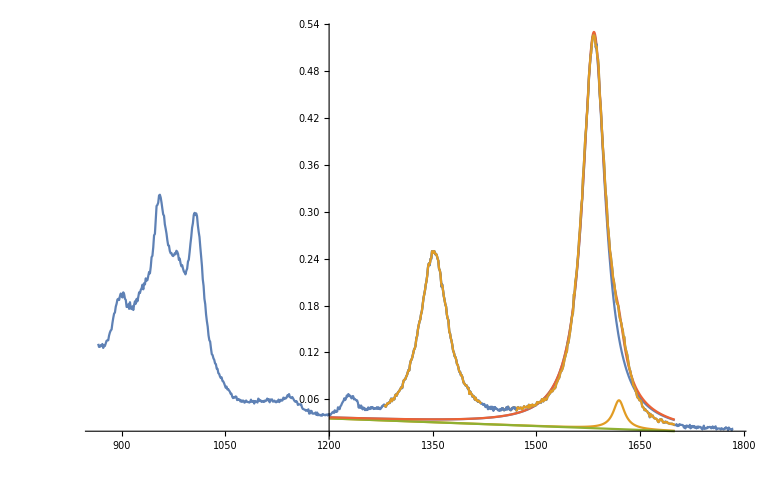

```mathematica
soln1=Solve[fit1==halfmax1,{x}]
FWHM1=soln1[[2]][[1]][[2]]-soln1[[1]][[1]][[2]]
max1=(soln1[[2]][[1]][[2]]+soln1[[1]][[1]][[2]])/2
soln2=Solve[fit2==halfmax2,{x}]
FWHM2=soln2[[2]][[1]][[2]]-soln2[[1]][[1]][[2]]
max2=(soln2[[2]][[1]][[2]]+soln2[[1]][[1]][[2]])/2

Show[{Plot[{fit1+correction,fit2+correction,correction,fit1+fit2+correction},{x,1200,1700},PlotRange->All],graphiteP,graphiteP2}]
```

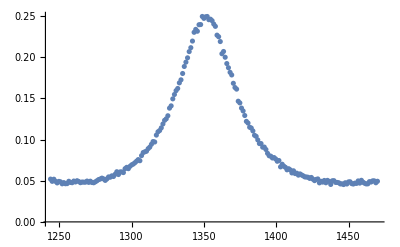

```mathematica
ListPlot@graphite2
```

InterpolatingFunction[{{1243.96, 1470.01}}, <>]

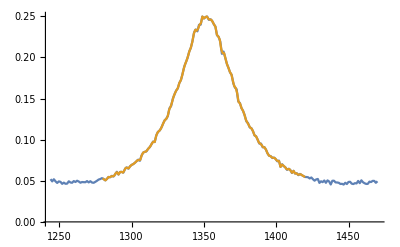

```mathematica
graphite2=Transpose[{Transpose[expRaman][[1]],Transpose[expRaman][[3]]}][[500;;700]];
graphiteInt2=Interpolation[graphite2]
graphiteTab2=Table[{x,graphiteInt2[x]},{x,1280,1420}];
graphiteP2=ListLinePlot[{graphite2,graphiteTab2},PlotRange->All]
```

```mathematica
fit=c/(b π (1+(-a+x)^2/b^2))/.{a->1588.5612507350584,b->36.66281023168635,c->17.758257775896872}
fitB=g/(e π (1+(-d+x)^2/e^2))/.{d->1582.3222283802925,e->17.912135399752202,g->21.22783069435452}
```

```mathematica
lim=(fit/.x->1588.5612507350584)/2
soln=Solve[fit==lim,{x}]
soln[[2]][[1]][[2]]-soln[[1]][[1]][[2]]

limB=(fitB/.x->1582.3222283802925)/2
solnB=Solve[fitB==limB,{x}]
solnB[[2]][[1]][[2]]-solnB[[1]][[1]][[2]]
```

0.0770894

{{x→1551.9},{x→1625.22}}

73.3256

0.188616

{{x→1564.41},{x→1600.23}}

35.8243

```mathematica
edist=NonlinearModelFit[graphiteTab,model[x],{a,b,c,d,e,g},x]
edist[[1]]
```

FittedModel[0.154179/(1+0.000743958 (-«19»+x)^2)+0.377232/(1+«22» («1»)^2)]

{Nonlinear,{a→1588.56,b→36.6628,c→17.7583,d→1582.32,e→17.9121,g→21.2278},{{x},c/(b π (1+(-a+x)^2/b^2))+g/(e π (1+(-d+x)^2/e^2))}}

```mathematica
edist2=NonlinearModelFit[graphiteTab2,c*model[x],{a,b,c},x];
edist2[[1]];
```

0.0770894

{{x→1551.9},{x→1625.22}}

73.3256

0.188616

{{x→1564.41},{x→1600.23}}

35.8243

```mathematica
edist2[1351.5548953244042]/2
soln2=Solve[edist2[x]==edist2[1351.5548953244042]/2,{x}]
soln2[[2]][[1]][[2]]-soln2[[1]][[1]][[2]]
```

0.119694

{{x→1320.39},{x→1382.72}}

62.3363

```mathematica
fitA+fitB
```

fitA+0.377232/(1+0.00311677 (-1582.32+x)^2)

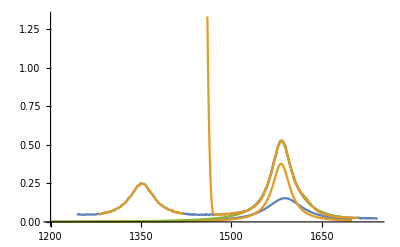

```mathematica
Show[{Plot[{fit,fitB,fit+fitB},{x,1200,1700},PlotRange->All],graphiteP,graphiteP2}]
```

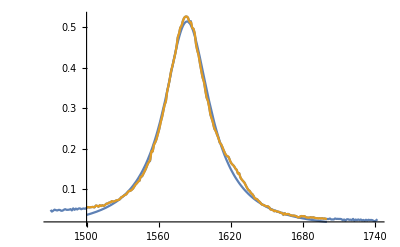

```mathematica
Show[{Plot[edist[x],{x,1500,1700},PlotRange->All],graphiteP}]
```

```mathematica
Plot[PDF[edist,x],{x,0,1600}]
```

-Graphics-

```mathematica
FindDistributionParameters[graphite,CauchyDistribution[n,p]]
```

FindDistributionParameters::ntsprt: One or more data points are not in support of the process or distribution CauchyDistribution[n,p].

FindDistributionParameters[{{1688.58,0.0312674},{1687.51,0.0303149},{1686.43,0.0316875},{1685.36,0.0299604},{1684.28,0.0308162},{1683.21,0.0302086},{1682.13,0.0325269},{1681.05,0.0343282},{1679.98,0.0332042},{1678.9,0.0344888},{1677.83,0.0331931},{1676.75,0.0306942},{1675.67,0.0315487},{1674.6,0.0338641},{1673.52,0.0348037},{1672.44,0.0354853},{1671.37,0.0353935},{1670.29,0.0359029},{1669.21,0.0370133},{1668.13,0.0392396},{1667.05,0.0393189},{1665.97,0.0381106},{1664.9,0.0414513},{1663.82,0.0368966},{1662.74,0.0424669},{1661.66,0.0418594},{1660.58,0.0442538},{1659.5,0.0450181},{1658.42,0.0453535},{1657.34,0.0475747},{1656.26,0.0459383},{1655.18,0.0490156},{1654.1,0.0500355},{1653.02,0.0506268},{1651.94,0.0560998},{1650.86,0.0582313},{1649.78,0.0585641},{1648.7,0.0588967},{1647.62,0.0616258},{1646.53,0.0618722},{1645.45,0.0639154},{1644.37,0.0685243},{1643.29,0.0709934},{1642.21,0.0748299},{1641.12,0.0768696},{1640.04,0.0775406},{1638.96,0.0841094},{1637.87,0.0886249},{1636.79,0.0910026},{1635.71,0.0966261},{1634.62,0.0985746},{1633.54,0.104024},{1632.46,0.11024},{1631.37,0.116881},{1630.29,0.120276},{1629.2,0.124182},{1628.12,0.128599},{1627.03,0.139925},{1625.95,0.139134},{1624.86,0.148748},{1623.78,0.151538},{1622.69,0.157651},{1621.61,0.160694},{1620.52,0.164247},{1619.43,0.17027},{1618.35,0.179444},{1617.26,0.181884},{1616.17,0.183728},{1615.09,0.189829},{1614.,0.19729},{1612.91,0.20526},{1611.83,0.212205},{1610.74,0.215574},{1609.65,0.227706},{1608.56,0.23473},{1607.47,0.244558},{1606.38,0.248939},{1605.3,0.263184},{1604.21,0.274362},{1603.12,0.283497},{1602.03,0.303338},{1600.94,0.318923},{1599.85,0.326771},{1598.76,0.345661},{1597.67,0.366242},{1596.58,0.375097},{1595.49,0.39261},{1594.4,0.409523},{1593.31,0.43008},{1592.22,0.441465},{1591.13,0.456664},{1590.04,0.484414},{1588.95,0.496293},{1587.86,0.498075},{1586.76,0.514866},{1585.67,0.510541},{1584.58,0.522746},{1583.49,0.525964},{1582.4,0.526045},{1581.3,0.523416},{1580.21,0.515958},{1579.12,0.503591},{1578.03,0.499019},{1576.93,0.48395},{1575.84,0.474134},{1574.74,0.449171},{1573.65,0.432256},{1572.56,0.418561},{1571.46,0.403856},{1570.37,0.392793},{1569.27,0.372431},{1568.18,0.355543},{1567.08,0.341704},{1565.99,0.316627},{1564.89,0.308208},{1563.8,0.292102},{1562.7,0.276677},{1561.61,0.264974},{1560.51,0.248799},{1559.41,0.237696},{1558.32,0.225077},{1557.22,0.216176},{1556.13,0.210907},{1555.03,0.193574},{1553.93,0.194132},{1552.83,0.169974},{1551.74,0.168006},{1550.64,0.160725},{1549.54,0.152267},{1548.44,0.145245},{1547.34,0.139152},{1546.25,0.13205},{1545.15,0.132365},{1544.05,0.121307},{1542.95,0.119603},{1541.85,0.115035},{1540.75,0.112069},{1539.65,0.106662},{1538.55,0.101678},{1537.45,0.0987998},{1536.35,0.0962589},{1535.25,0.0959904},{1534.15,0.0925256},{1533.05,0.0878846},{1531.95,0.0863563},{1530.85,0.08424},{1529.75,0.0817882},{1528.65,0.0801777},{1527.54,0.0752065},{1526.44,0.0740176},{1525.34,0.0733332},{1524.24,0.0722291},{1523.14,0.0702016},{1522.04,0.0701898},{1520.93,0.0711015},{1519.83,0.0675644},{1518.73,0.0677209},{1517.62,0.0648569},{1516.52,0.0650976},{1515.42,0.061564},{1514.31,0.0591217},{1513.21,0.0612079},{1512.1,0.0589342},{1511.,0.0609359},{1509.89,0.0571545},{1508.79,0.0595748},{1507.69,0.0601513},{1506.58,0.0554505},{1505.47,0.0568649},{1504.37,0.0564367},{1503.26,0.0560086},{1502.16,0.055497},{1501.05,0.0565757},{1499.95,0.0543905},{1498.84,0.0521225},{1497.73,0.0529502},{1496.63,0.0523559},{1495.52,0.0511764},{1494.41,0.053258},{1493.3,0.0528311},{1492.2,0.050482},{1491.09,0.0527298},{1489.98,0.0496295},{1488.88,0.0532133},{1487.77,0.0481094},{1486.66,0.0513582},{1485.55,0.0500972},{1484.44,0.0496713},{1483.33,0.049663},{1482.22,0.0513237},{1481.11,0.0498132},{1480.,0.0476358},{1478.89,0.0472941},{1477.78,0.0493711},{1476.67,0.0494462},{1475.56,0.0480206},{1474.45,0.0489294},{1473.34,0.050088},{1472.23,0.0474964},{1471.12,0.0453223},{1470.01,0.0493964}},CauchyDistribution[n,p]]

```mathematica
?Lorentzian
```

Information::notfound: Symbol Lorentzian not found.

```mathematica
names
```

{perf,fren129,fren142,fren70,fren174,fren1126,cvac}

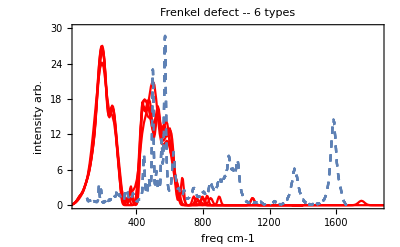

```mathematica
Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],Frame->True,FrameLabel->{"freq cm-1","intensity arb."},PlotStyle->Red,PlotRange->{{50,1850},{0,30}},PlotLabel->"Frenkel defect -- 6 types"],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,2,6,1}]//Show
```

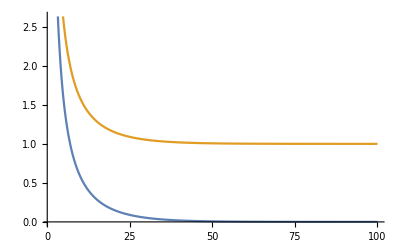

```mathematica
With[{T=10},Plot[{(1/(Exp[omega/T]-1)),(1/(Exp[omega/T]-1))+1},{omega,1,100}]]
```

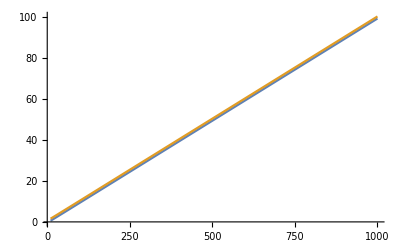

```mathematica
With[{omega=10},Plot[{(1/(Exp[omega/T]-1)),(1/(Exp[omega/T]-1)+1)},{T,10,1000}]]
```

```mathematica
thzToKelvin=47.99243415908;
popBE[{waveNum_,Intensity_},temp_,scale_]:={waveNum,scale*Intensity/(Exp[waveNum*(thzToKelvin/thz2waavenum)/temp]-1)waveNum^2}
```

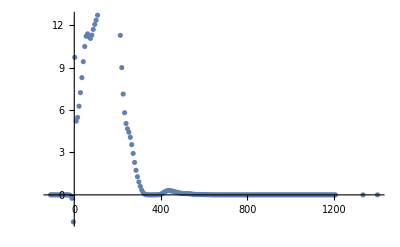

```mathematica
ListPlot@Table[popBE[data2D[[2]][[6]][[i]],100,10],{i,1,Length@data2D[[2]][[6]]}]
```

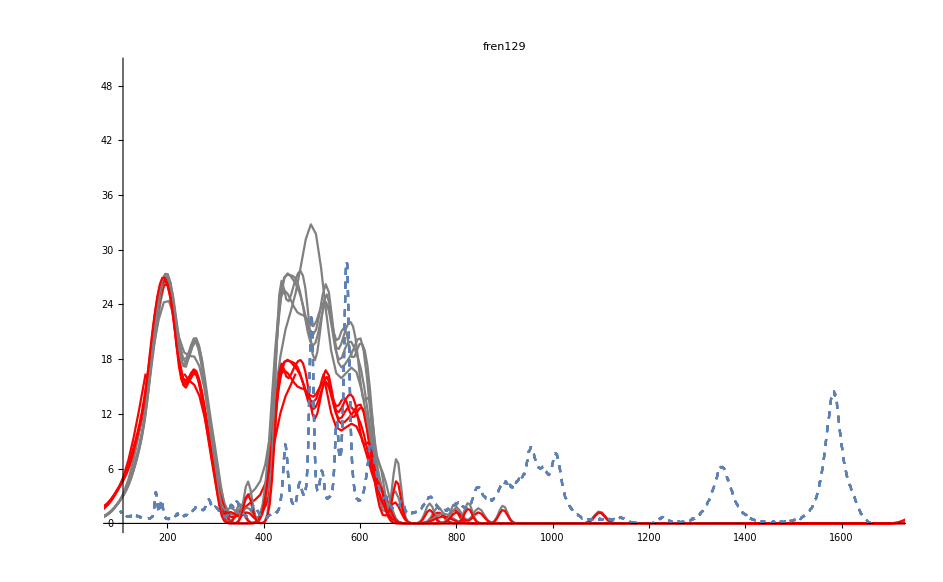

```mathematica
Table[With[{defect=i,vol=6},Show[{ListLinePlot[Table[popBE[data2D[[defect]][[vol]][[i]],500,0.00002],{i,1,203}],PlotRange->{{100,1700},{0,50}},PlotStyle->Gray,PlotLabel->names[[defect]]],ListLinePlot[data2D[[defect]][[vol]],PlotStyle->Red],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,2,6,1}]//Show
```

#### Perfect DOS and Raman

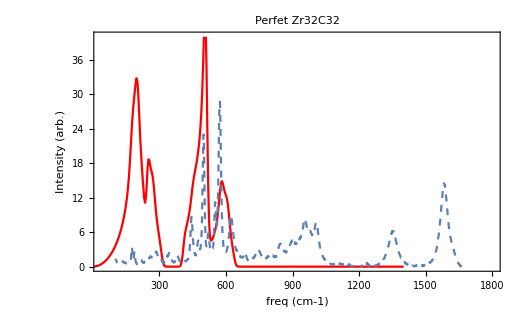

```mathematica
With[{defect=1,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{40,1800},{0,40}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]]
```

#### Perfect DOS convolution

```mathematica
(*ListPlot@Sum[Table[data2D[[1]][[6]][[j]]+data2D[[1]][[6]][[i]],{i,1,203}],{j,1,200}];
ListPlot@Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,40,75}];
jFun[x_,arg_]:=If[x<arg[[1]][[1]],0,Evaluate[If[x>arg[[-1]][[1]],0,Interpolation[arg][x]]]]
test=Table[jFun[x,Table[Table[{Transpose[data2D[[1]][[6]]][[1]][[i]]+Transpose[data2D[[1]][[6]]][[1]][[j]],Transpose[data2D[[1]][[6]]][[2]][[i]]+Transpose[data2D[[1]][[6]]][[2]][[j]]},{i,1,200}],{j,1,200}][[k]]],{k,1,200}];
sum=Total@Table[test[[i]],{i,0,20}]
allJDos=Table[test[[i]]/.x->y,{i,1,200}]
finalJDOS=Table[{i,Total[allJDos/.y->i//N]},{i,1,1400,10}];
j=Interpolation[finalJDOS]
Plot[j[x],{x,0,1400}]*)
```

#### CVAC DOS and Raman

```mathematica
data2D[[1]][[1]];
```

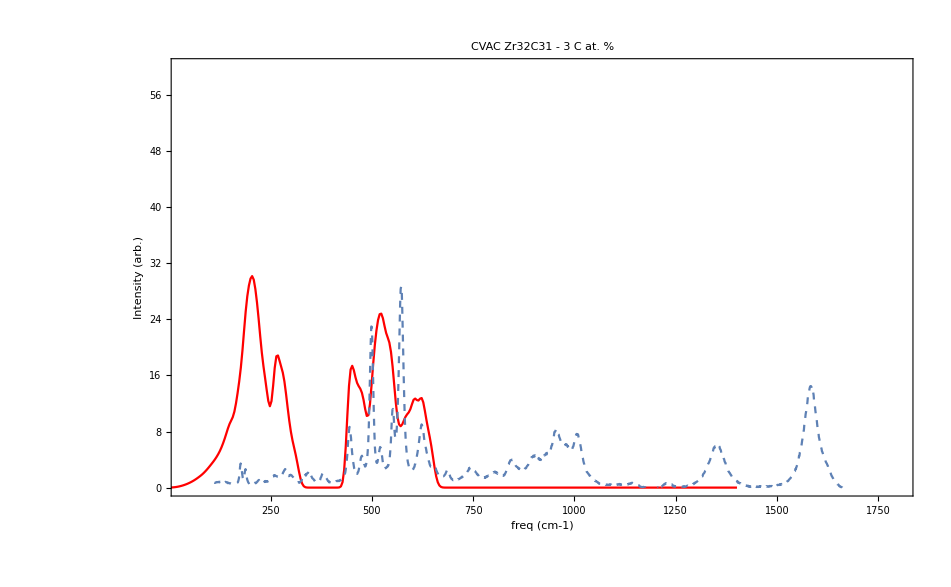

```mathematica
With[{defect=7,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{40,1800},{0,60}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]]
```

```mathematica
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.5,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotLegends->Placed[{"Exp"},{0.5,0.7}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

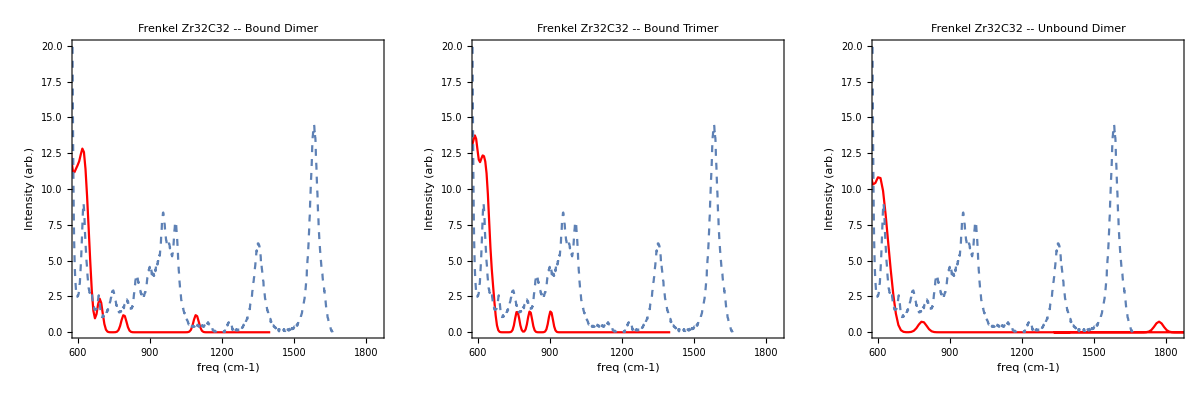

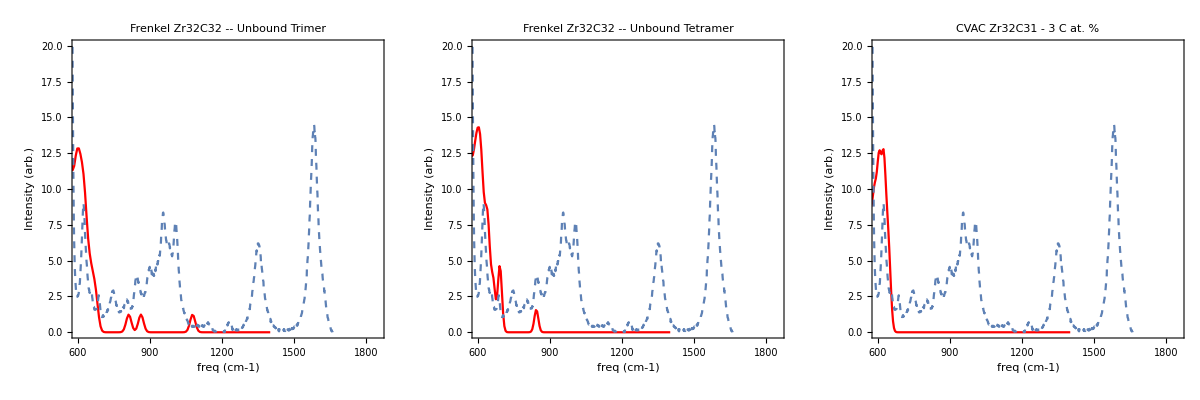

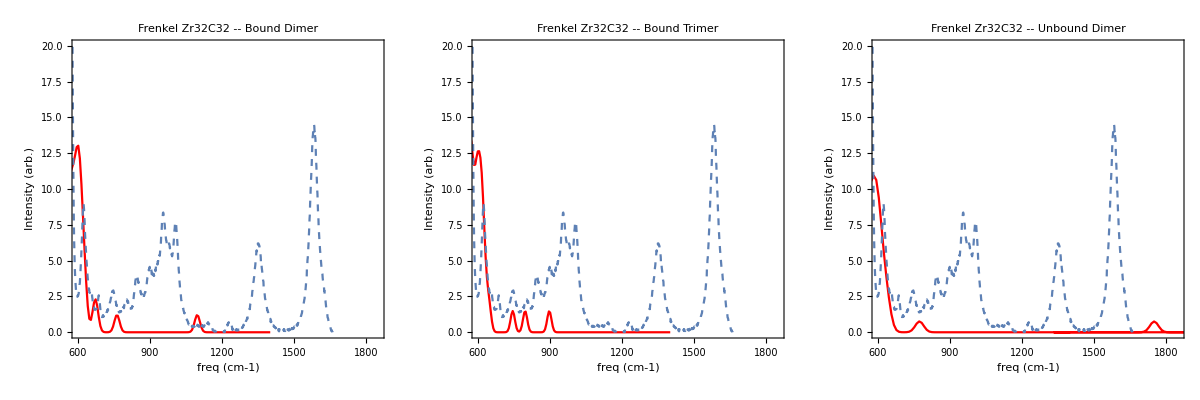

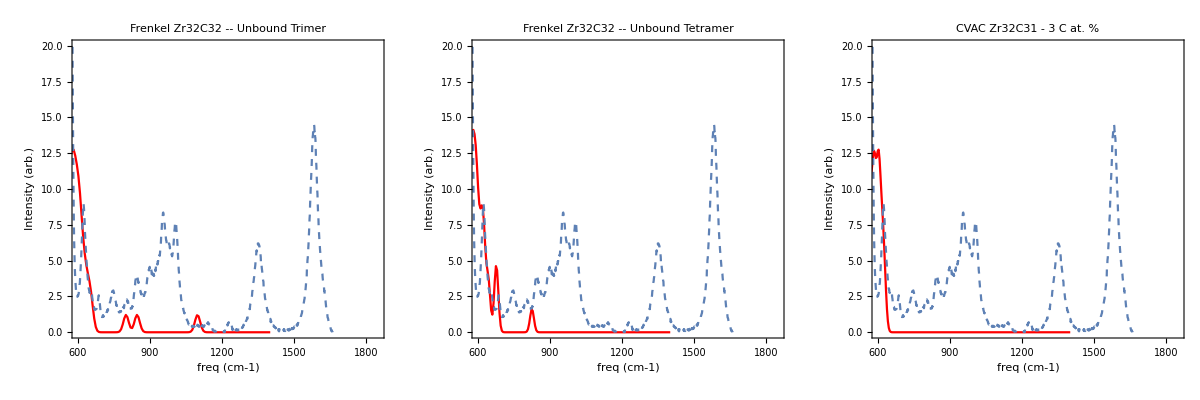

```mathematica
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.5,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{600,1850},{0,20}},Frame->True,FrameLabel->{"freq (cm-1)","Intensity (arb.)"},PlotLegends->Placed[{"DFT"},{0.5,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotLegends->Placed[{"Exp"},{0.5,0.7}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

#### Concentration at 300 K and at 3000K

```mathematica
(*Concentration says:U3, then U2 and U4, then B2 and B3.*)
```

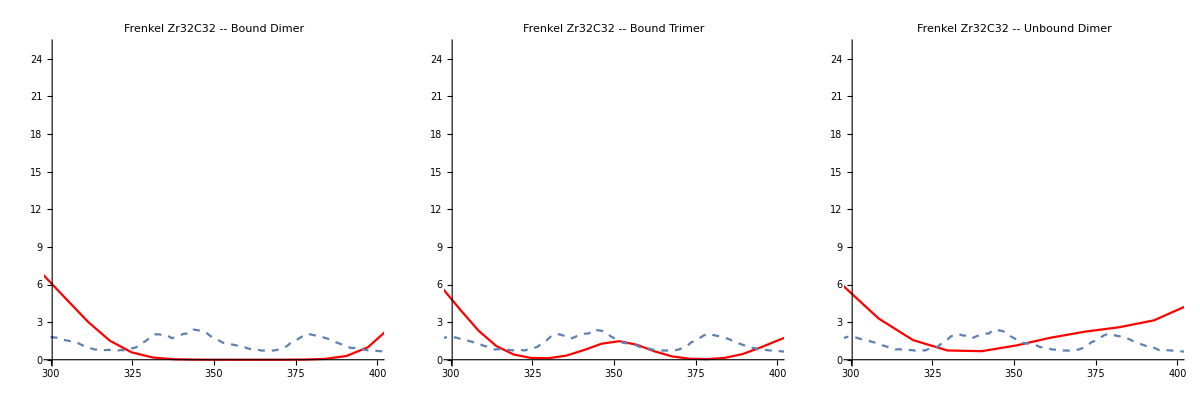

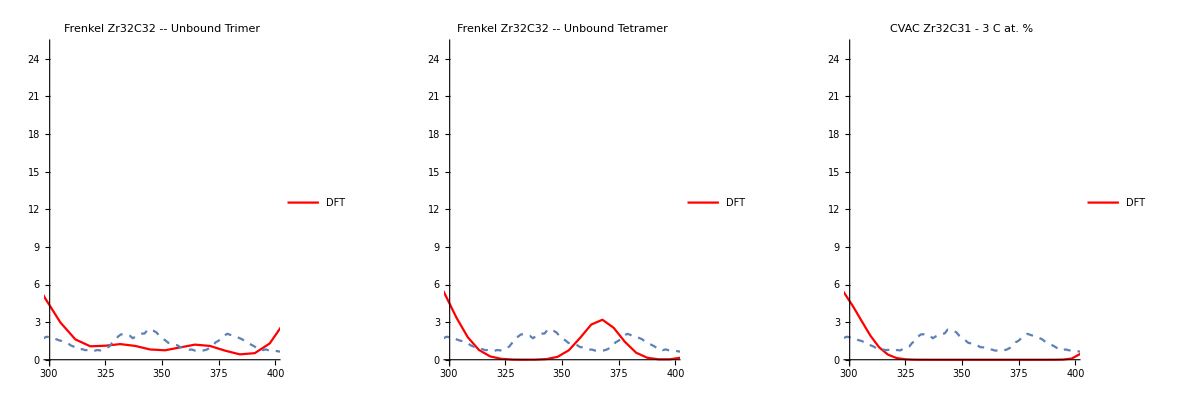

```mathematica
Gap states;
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{300,400},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=6},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{300,400},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```

Carbon states

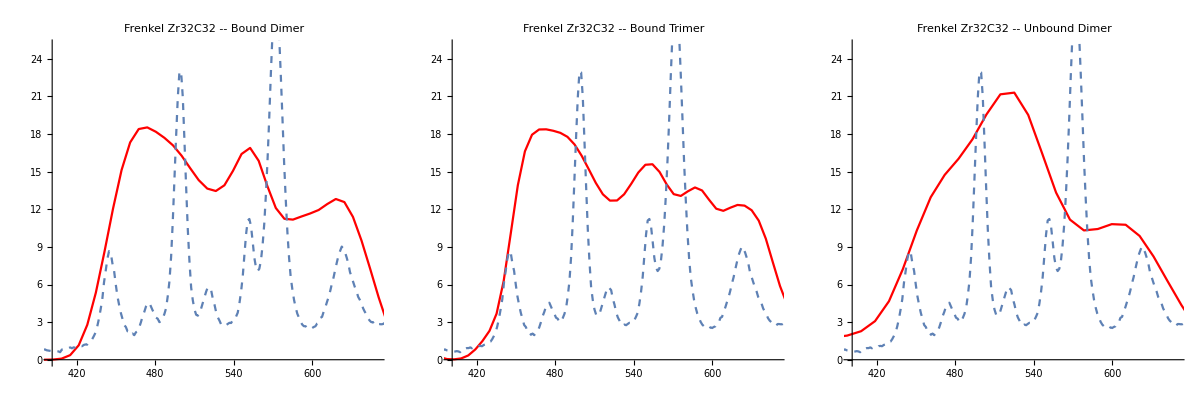

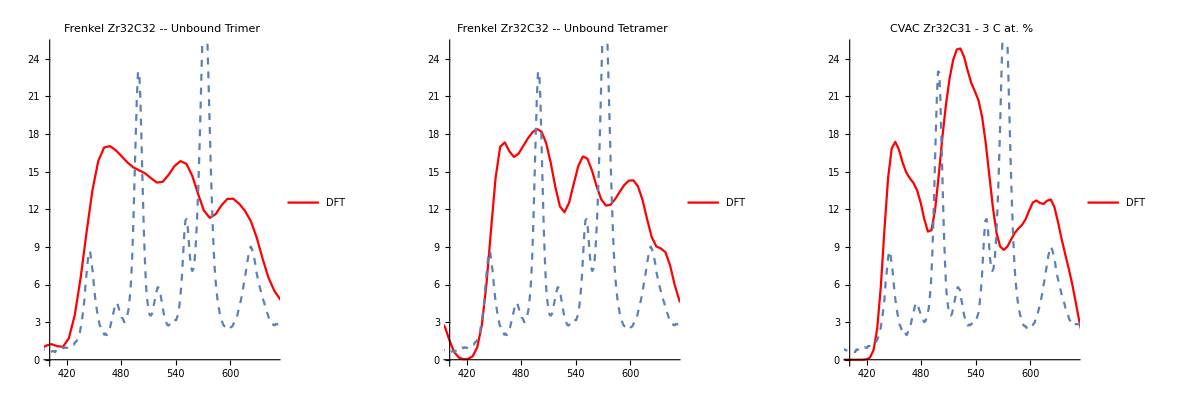

```mathematica
Carbon states
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{400,650},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed,PlotLegends->Placed[{"Exp"},{0.7,0.7}]]}]],{i,2,4,1}]},ImageSize->1200,Spacings->0]
GraphicsGrid[{Table[With[{defect=i,vol=5},Show[{ListLinePlot[data2D[[defect]][[vol]],PlotRange->{{400,650},{0,25}},PlotLegends->Placed[{"DFT"},{0.7,0.7}],PlotStyle->Red,PlotLabel->names2[[defect]]],ListLinePlot[Transpose[{Transpose[expRaman][[1]],30*Transpose[expRaman][[3]]-1.3}],PlotRange->{{100,1200},{0,30}},PlotStyle->Dashed]}]],{i,5,7,1}]},ImageSize->1200,Spacings->0]
```